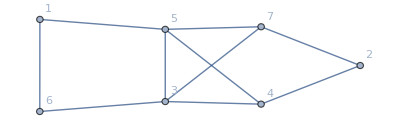

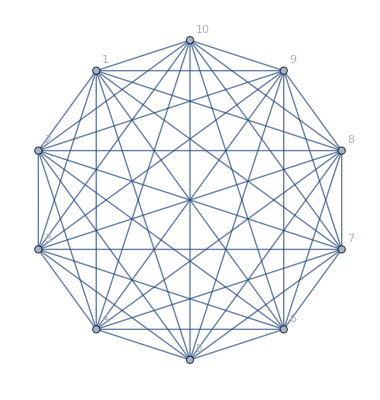

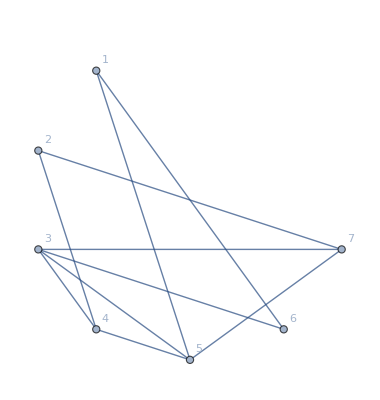

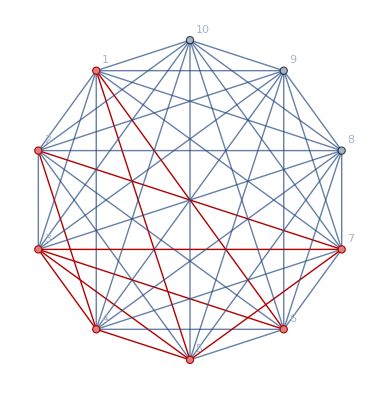

```mathematica
rg=Graph[RandomGraph[{7,10}],VertexLabels->"Name"]
n=VertexCount[rg];
cmp=Graph[CompleteGraph[10],VertexLabels->"Name"]
(*cmp=CompleteGraph[n];*)
HighlightGraph[cmp,rg,GraphHighlightStyle->"DehighlightHide",VertexLabels->"Name"]
HighlightGraph[cmp,rg,GraphHighlightStyle->"Thick",VertexLabels->"Name"]
```